# Laplace egyenlet

## Általános megoldás

```mathematica
pde=Laplacian[u[x,y],{x,y}]==0
```

u^(0,2)[x,y]+u^(2,0)[x,y]==0

```mathematica
DSolve[pde,u,{x,y}]
```

{{u→Function[{x,y},C[1][ⅈ x+y]+C[2][-ⅈ x+y]]}}

## Peremfeltételekkel fűszerezve

#### Szimpla kezdeti feltétel (ezt nem tudja megoldani)

```mathematica
(* Laplace egyenlet *)
pde=Laplacian[u[x,y],{x,y}]==0;

(* Peremfeltetelek *)
bc={u[0,y]==0,u[1,y]==0,u[x,0]==0,u[x,1]==Sin[Pi*x]};

(* PDE megoldasa *)
solA=u[x,y]/.DSolve[{pde,bc},u[x,y],{x,y}][[1]]
```

0K[1]1∞

#### (2a)

```mathematica
(* Laplace egyenlet *)
pde=Laplacian[u[x,y],{x,y}]==0;

(* Peremfeltetelek *)
bc={u[0,y]==0,u[1,y]==0,u[x,0]==0,u[x,1]==1};

(* PDE megoldasa *)
solA=u[x,y]/.DSolve[{pde,bc},u[x,y],{x,y}][[1]];
StringForm["Megoldás: ``",solA//TraditionalForm]
```

Megoldás: 2/π

```mathematica
(* Boundary condition - line-ja: *)
l=Line[{{1,1,0},{1,0,0},{0,0,0},{0,1,0},{0,1,1},{1,1,1},{1,1,0}}];
r2=Graphics3D[{Red,Thickness[0.01],l}];
```

```mathematica
(* Inactive SUM *)
nr=1000;
fsolA=solA/.∞->nr//Activate;
r1=Plot3D[fsolA//Evaluate,{x,0,1},{y,0,1},PlotRange->All];
Show[r1,r2]
```

-Graphics3D-

```mathematica
fsolA20=solA/.∞->20//Activate;
r20=Plot3D[fsolA20//Evaluate,{x,0,1},{y,0,1},PlotRange->All];
fsolA200=solA/.∞->200//Activate;
r200=Plot3D[fsolA200//Evaluate,{x,0,1},{y,0,1},PlotRange->All];
GraphicsGrid[{{Show[r2,r20],Show[r2,r200]}}]
```

-Graphics-

#### (2b)

```mathematica
(* Laplace egyenlet *)
pde=Laplacian[u[x,y],{x,y}]==0;

(* Peremfeltetelek *)
bc={u[0,y]==0,u[1,y]==1,u[x,0]==0,u[x,1]==0};

(* PDE megoldasa *)
solB=u[x,y]/.DSolve[{pde,bc},u[x,y],{x,y}][[1]];
StringForm["Megoldás: ``",solB//TraditionalForm]
```

Megoldás: 2/π

```mathematica
(* Boundary condition - line-ja: *)
l=Line[{{1,1,0},{1,0,0},{0,0,0},{0,1,0},{0,1,1},{1,1,1},{1,1,0}}];
r2=Graphics3D[{Red,Thickness[0.01],l}];
```

```mathematica
(* Inactive SUM *)
fsolB=solB/.∞->nr//Activate;
r1=Plot3D[fsolB//Evaluate,{x,0,1},{y,0,1},PlotRange->All];
Show[r1,r2]
```

-Graphics3D-

#### (2c)

```mathematica
solC=solA+solB
```

(2 (1+(-1)^(1+K[1])) Csch[π K[1]] Sin[π y K[1]] Sinh[π x K[1]])/(π K[1])K[1]1∞+(2 (1+(-1)^(1+K[1])) Csch[π K[1]] Sin[π x K[1]] Sinh[π y K[1]])/(π K[1])K[1]1∞

```mathematica
(* Inactive SUM *)
fsolC=solC/.∞->nr//Activate;
r1=Plot3D[fsolC//Evaluate,{x,0,1},{y,0,1},PlotRange->All];
Show[r1,r2]
```

-Graphics3D-

#### No, akkor játszunk is egy kicsit...

```mathematica
(* Laplace egyenlet *)
pde=Laplacian[u[x,y],{x,y}]==0;

(* Peremfeltetelek *)
bc={u[0,y]==10y-5,u[1,y]==y^2,u[x,0]==-(2x)^2,u[x,1]==3Sin[10x]};

(* PDE megoldasa *)
solD=u[x,y]/.DSolve[{pde,bc},u[x,y],{x,y}][[1]];
(* Inactive SUM *)
fsolD=solD/.∞->nr//Activate;
r1=Plot3D[fsolD//Evaluate,{x,0,1},{y,0,1},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

Igy kellene hasznalni a map-eket...

```mathematica
Show[ParametricPlot3D[
{bc[[#,1,1]],bc[[#,1,2]],bc[[#,2]]},{x,0,1},{y,0,1},PlotStyle->Red,PlotRange->{{0,1},{0,1},{-1,1}}]&/@Range[4]];
```

```mathematica
{bc[[#,1,1]],bc[[#,1,2]],bc[[#,2]]}&/@Range[4];
```

```mathematica
bc[[#]]&/@Range[4];
```

## Durvább peremfeltételekkel fűszerezve (beletörik a bicskája)

```mathematica
(* Laplace egyenlet *)
pde=Laplacian[u[x,y],{x,y}]==0;

(* Peremfeltetelek *)
bc5Der={u[0,y]==0,u[1,y]==0,Derivative[0,1][u][x,0]==0,u[x,1]==x^2-x};
bc5Normal={u[0,y]==0,u[1,y]==0,u[x,0]==b[x],u[x,1]==x^2-x};
sol5Der=DSolve[{pde,bc5Der},u[x,y],{x,y}];
sol5Normal=DSolve[{pde,bc5Normal},u[x,y],{x,y}];
```

```mathematica
StringForm["Peremfeltételek: ``\nEzzel a DSolve nem tud mit kezdeni:\n``,\nezért fogalmazzuk ezt át egy ezzel ekvivalens peremfeltétellé, ahol nem szerepelnek a deriváltak: ``, b(x) egy tetszőleges függvény.\nA megoldása pedig:\nu[x,y] = ``\nMegjegyzem, hogy a következő példa esetén (Euler-Tricomi egyenlet, ami már nem része a tanagyagnak), ott működik az ilyen típusú peremfeltétel. Tény, hogy az a feladat jól kondícionált és létezik egyértelmű megoldása. Erről ez nem mondható el.", bc5Der,sol5Der,bc5Normal,sol5Normal[[1,1,2]]]
(* PDE megoldasa *)
```

Peremfeltételek: {u[0,y]==0,u[1,y]==0,u^(0,1)[x,0]==0,u[x,1]==-x+x^2}
Ezzel a DSolve nem tud mit kezdeni:
DSolve[{u^(0,2)[x,y]+u^(2,0)[x,y]==0,{u[0,y]==0,u[1,y]==0,u^(0,1)[x,0]==0,u[x,1]==-x+x^2}},u[x,y],{x,y}],
ezért fogalmazzuk ezt át egy ezzel ekvivalens peremfeltétellé, ahol nem szerepelnek a deriváltak: {u[0,y]==0,u[1,y]==0,u[x,0]==b[x],u[x,1]==-x+x^2}, b(x) egy tetszőleges függvény.
A megoldása pedig:
u[x,y] = (
Megjegyzem, hogy a következő példa esetén (Euler-Tricomi egyenlet, ami már nem része a tanagyagnak), ott működik az ilyen típusú peremfeltétel. Tény, hogy az a feladat jól kondícionált és létezik egyértelmű megoldása. Erről ez nem mondható el.

```mathematica
h[x_]=x^2-x;
FourierSinSeries[h[Pi x],x,3]
```

2 π (-5+π^2) Sin[x]+(π-π^3) Sin[2 x]+2/27 π (-13+9 π^2) Sin[3 x]

### Bezzeg ezt megeszi:

```mathematica
TricomiEqn=D[u[x,y],{x,2}]+y D[u[x,y],{y,2}]==0;
DSolve[{TricomiEqn,u[x,0]==0, Derivative[0,1][u][x,0]==x^2},u[x,y],{x,y}]
Plot3D[u[x,y]/.%[[1]]//Evaluate, {x,-3,3},{y,0,5}]
```

{{u[x,y]→-y (-x^2+y)}}

-Graphics3D-

# Egyoldali Fourier sorfejtés

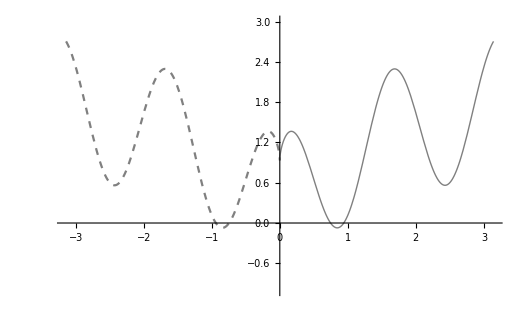

```mathematica
(* Van egy függvény, azt kiterjesztjük úgy, hogy páros/páratlan legyen: *)
funOrig[x_]=Sin[4x+1.2]+√x;
fun=funOrig[Abs[x]];

p1=Plot[fun,{x,0,Pi},PlotStyle->{Thick,Gray}];
p2=Plot[fun,{x,-Pi,0},PlotStyle->{Dashed,Gray}];
Show[p1,p2,PlotRange->{{-Pi,Pi},{-1,3}}]
```

```mathematica
(* Fourier sorfejtése ennek a ronda függvénynek *)
nr=20;

(* Igy is jo, csak nagyon lassu *)
(* fser=FourierSeries[fun,x,nr]; *)
(* fserCos=TrigReduce[ExpToTrig[%]] *)

fserCos=FourierCosSeries[funOrig[x],x,nr]
```

1.18164-0.446636 Cos[x]-0.0968758 Cos[2 x]+0.167063 Cos[3 x]+0.893345 Cos[4 x]-0.247897 Cos[5 x]-0.0221663 Cos[6 x]-0.0811237 Cos[7 x]-0.0148282 Cos[8 x]-0.0453826 Cos[9 x]-0.0108211 Cos[10 x]-0.0299943 Cos[11 x]-0.00835058 Cos[12 x]-0.0216354 Cos[13 x]-0.00669994 Cos[14 x]-0.016495 Cos[15 x]-0.00553217 Cos[16 x]-0.0130729 Cos[17 x]-0.00466983 Cos[18 x]-0.0106636 Cos[19 x]-0.00401143 Cos[20 x]

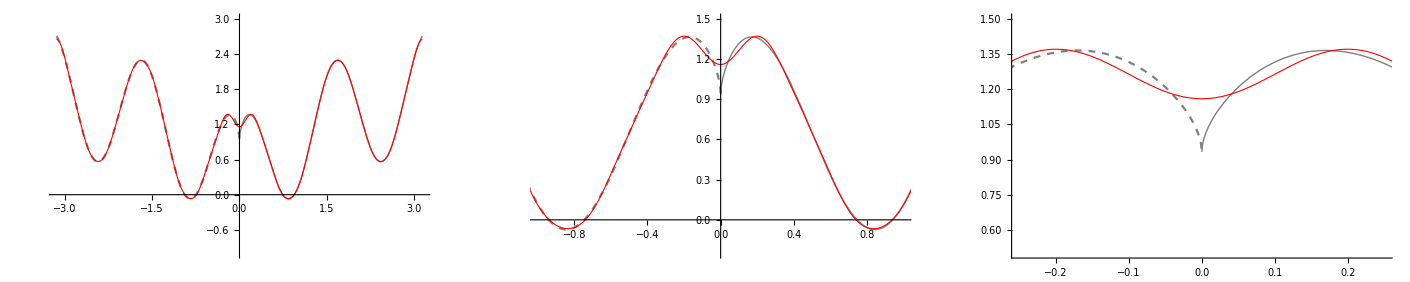

```mathematica
fserCosParts=Array[Take[fserCos,#1]&,nr];
Manipulate[Show[p1,p2,Plot[fserCosParts[[n]],{x,-Pi,Pi},PlotStyle->{Red,Thickness[0.002]}]],{n,1,nr,1}];
GraphicsGrid[{Show[p1,p2,Plot[fserCosParts[[nr]],{x,-Pi,Pi},PlotStyle->{Red,Thickness[0.002]}], PlotRange->{{-#[[1]],#[[1]]},{#[[2]],#[[3]]}}]&/@{{Pi,-1,3},{1,-0.25,1.5},{0.25,0.5,1.5}}}]
```

## További Fourier példák

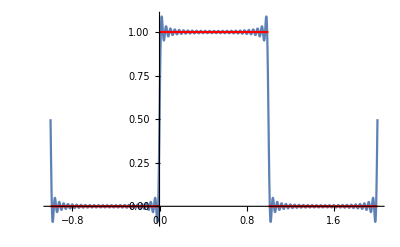

```mathematica
(* A FourierSeries sajnos buta, csak [-Pi,Pi] intervallumon tud sort fejteni. Ezert traszformalni kell a fuggvenyt ennek megfeleloen. *)
g[x_]=UnitBox[x-0.5];
f[x_]=FourierSeries[g[x/Pi],x,50];
s1=Plot[f[x Pi],{x,-1,2},PlotRange->Full];
s2=Plot[g[x],{x,-1,2},PlotRange->Full,PlotStyle->Red];
Show[s1,s2]
```

## FourierCosSeries - ha a függvény eleve páros

1/2+(4 Cos[x])/π^2+(4 Cos[3 x])/(9 π^2)

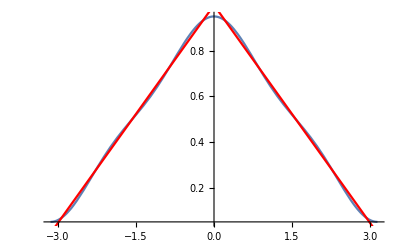

1/2+(4 Cos[x])/π^2+(4 Cos[3 x])/(9 π^2)

```mathematica
(* A FourierSeries sajnos buta, és csak [0,2Pi] intervallumon tud sort fejteni. Ezert traszformalni kell a fuggvenyt ennek megfeleloen. *)
g[x_]=1-Abs[x]/Pi;
f[x_]=ExpToTrig[FourierSeries[g[x],x,3]]
s1=Plot[f[x],{x,-Pi,Pi},PlotRange->Full];
s2=Plot[g[x],{x,-Pi,Pi},PlotRange->Full,PlotStyle->Red];
Show[s1,s2]
FourierCosSeries[g[x],x,3]
```

## FourierCosSeries, ha a függvény nem páros

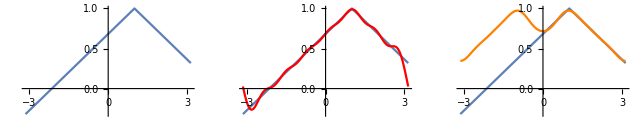

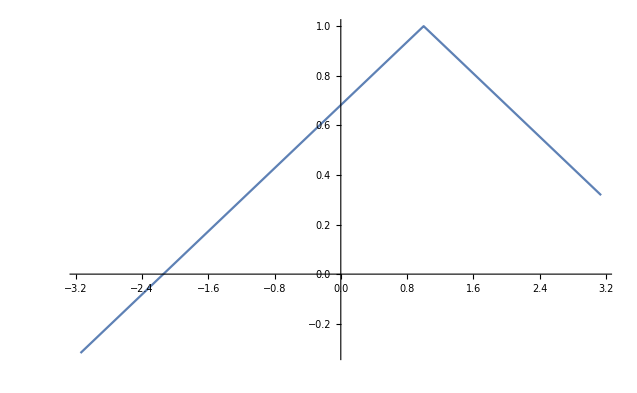

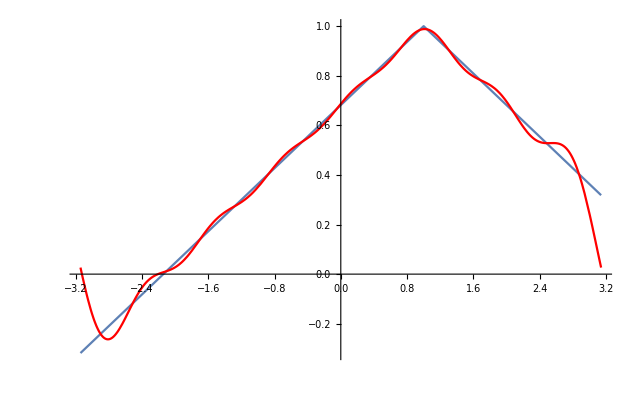

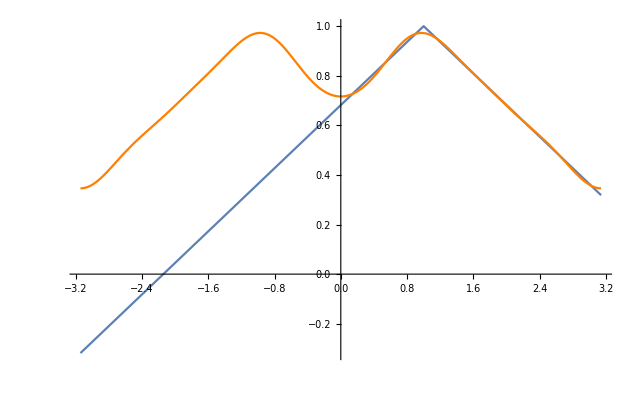

```mathematica
n=7;
g[x_]=1-Abs[x-1]/Pi;
f[x_]=ExpToTrig[FourierSeries[g[x],x,n]];
c[x_]=FourierCosSeries[g[x],x,n];
s1=Plot[g[x],{x,-Pi,Pi},PlotRange->Full];
s2=Plot[f[x],{x,-Pi,Pi},PlotRange->Full,PlotStyle->Red];
s3=Plot[c[x],{x,-Pi,Pi},PlotRange->Full,PlotStyle->Orange];
GraphicsGrid[{{Show[s1],Show[s1,s2],Show[s1,s3]}}]
Show[s1]
Show[s1,s2]
Show[s1,s3]
```

0.5+(0.+0.31831 ⅈ) (Cos[x]-ⅈ Sin[x])-(0.+0.31831 ⅈ) (Cos[x]+ⅈ Sin[x])+(0.+0.106103 ⅈ) (Cos[3 x]-ⅈ Sin[3 x])-(0.+0.106103 ⅈ) (Cos[3 x]+ⅈ Sin[3 x])+(0.+0.063662 ⅈ) (Cos[5 x]-ⅈ Sin[5 x])-(0.+0.063662 ⅈ) (Cos[5 x]+ⅈ Sin[5 x])

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)

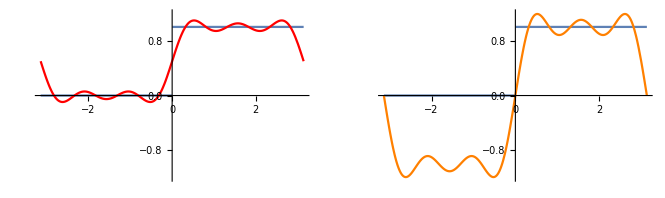

```mathematica
n=5;
g[x_]=UnitBox[x/Pi-0.5];
f[x_]=ExpToTrig[FourierSeries[g[x],x,n]]
c[x_]=FourierSinSeries[1,x,n]
s1=Plot[g[x],{x,-Pi,Pi},PlotRange->{Full,{-1.2,1.2}}];
s2=Plot[f[x],{x,-Pi,Pi},PlotRange->{Full,{-1.2,1.2}},PlotStyle->Red];
s3=Plot[c[x],{x,-Pi,Pi},PlotRange->{Full,{-1.2,1.2}},PlotStyle->Orange];
GraphicsGrid[{{Show[s1,s2],Show[s1,s3]}}]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)

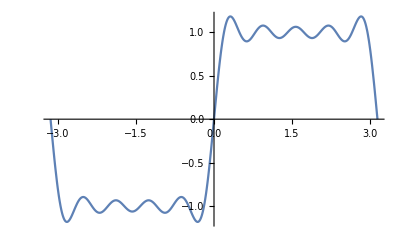

```mathematica
FourierSinSeries[1,x,10]
Plot[%,{x,-Pi,Pi}]
```

## Mathematica tricks

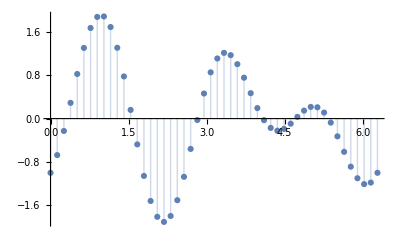

```mathematica
(* Apropo: Igy is lehet hasznalni az Array-t *)
ListPlot[Array[Sin[2 #]-Cos[3 #]&,50,{0,2 π}],Filling->Axis,DataRange->{0,2 π}]
```

Piecewise[{{Sin[π/6+4 x], -1<x<0}, {Sin[π/6-4 x], 0<x<1}, {0, True}}]

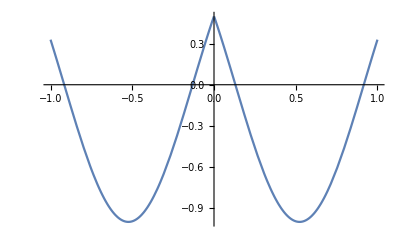

```mathematica
(* Piecewise függvényeket is lehet definiálni *)
fun=Piecewise[{{Sin[4x+Pi/6],-1<x<0},{Sin[4(-x)+Pi/6],0<x<1}}]
Plot[fun,{x,-1,1}]
```

```mathematica
vars=u@#&/@Range[3]
cons=Flatten@{Table[(u[j]≠#)&/@vars[[j+1;;-1]],{j,1,3-1}],1≤#≤3&/@vars}
vec1={1,2,3};vec2={1,2,3}
NMinimize[{Total@((vec1[[#]]-Indexed[vec2,u[#]])^2&/@Range[1,3]),cons},vars,Integers]
```

{u[1],u[2],u[3]}

{u[1]≠u[2],u[1]≠u[3],u[2]≠u[3],1≤u[1]≤3,1≤u[2]≤3,1≤u[3]≤3}

{1,2,3}

{0.,{u[1]→1,u[2]→2,u[3]→3}}

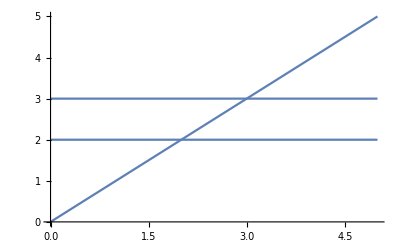
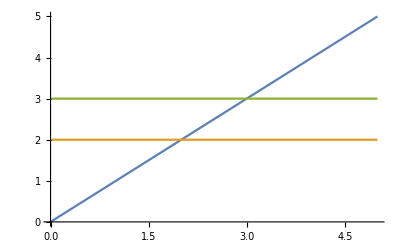

```mathematica
{Plot[functions[x,1,2,3][[#]]&/@{1,3,4}//Unevaluated,{x,0,5}],Plot[functions[x,1,2,3][[#]]&/@{1,3,4}//Evaluate,{x,0,5}]}
```